Show::gcomb: Could not combine the graphics objects in Show[,ErrorListPlot[{«1»}],,Frame→True,FrameLabel→{Projection Angle(ϕ),Maximum Height(h)},GridLines→Automatic,PlotLabel→Maximum Height(h) against Projection Angle(ϕ),ImageSize→500].

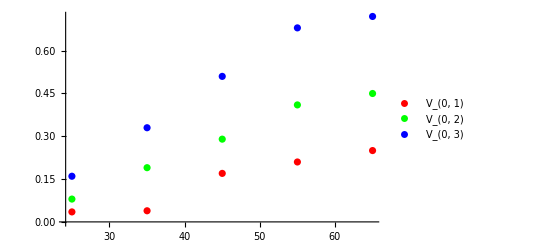
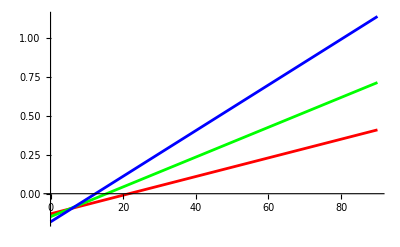
Show[-Graphics-,ErrorListPlot[{{{{25,0.035},ErrorBar[0,{0,0.005}]},{{35,0.039},ErrorBar[0,{0,0.005}]},{{45,0.17},ErrorBar[0,{0,0.02}]},{{55,0.21},ErrorBar[0,{0,0.02}]},{{65,0.25},ErrorBar[0,{0,0.02}]}},{{{25,0.08},ErrorBar[0,{0,0.01}]},{{35,0.19},ErrorBar[0,{0,0.015}]},{{45,0.29},ErrorBar[0,{0,0.02}]},{{55,0.41},ErrorBar[0,{0,0.025}]},{{65,0.45},ErrorBar[0,{0,0.03}]}},{{{25,0.16},ErrorBar[0,{0,0.015}]},{{35,0.33},ErrorBar[0,{0,0.02}]},{{45,0.51},ErrorBar[0,{0,0.025}]},{{55,0.68},ErrorBar[0,{0,0.03}]},{{65,0.72},ErrorBar[0,{0,0.035}]}}}],-Graphics-,Frame→True,FrameLabel→{Projection Angle(ϕ),Maximum Height(h)},GridLines→Automatic,PlotLabel→Maximum Height(h) against Projection Angle(ϕ),ImageSize→500]
V_(0, 1): y==0.00601 x-0.12965
V_(0, 2): y==0.0096 x-0.148
V_(0, 3): y==0.0147 x-0.1815

```mathematica
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

errorV1={{0,0.005},{0,0.005},{0,0.02},{0,0.02},{0,0.02}};
errorV2={{0,0.010},{0,0.015},{0,0.020},{0,0.025},{0,0.030}};
errorV3={{0,0.015},{0,0.020},{0,0.025},{0,0.030},{0,0.035}};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines*)
Column[{combinedPlot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],
ErrorListPlot[{Thread[{V1,ErrorBar[0,#]&/@errorV1}],Thread[{V2,ErrorBar[0,#]&/@errorV2}],Thread[{V3,ErrorBar[0,#]&/@errorV3}]}],
Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle(ϕ)","Maximum Height(h)"},GridLines->Automatic,PlotLabel->"Maximum Height(h) against Projection Angle(ϕ)",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

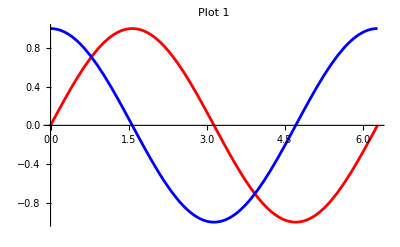

```mathematica
(*Example plots*)plot1=Plot[Sin[x],{x,0,2 Pi},PlotStyle->Red,PlotLabel->"Plot 1"];
plot2=Plot[Cos[x],{x,0,2 Pi},PlotStyle->Blue,PlotLabel->"Plot 2"];

(*Combine plots using Show*)
combinedPlot=Show[plot1,plot2,PlotRange->All];

(*Display the combined plot*)
combinedPlot
```

Thread::tdlen: Objects of unequal length in {{{25,0.035},{35,0.039},{45,0.17},{55,0.21},{65,0.25}},{{ErrorBar[0,0.005],ErrorBar[0,0.005],ErrorBar[0,0.002],ErrorBar[0,0.002],ErrorBar[0,0.002]}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{25,0.08},{35,0.19},{45,0.29},{55,0.41},{65,0.45}},{{ErrorBar[0,0.01],ErrorBar[0,0.015],ErrorBar[0,0.02],ErrorBar[0,0.025],ErrorBar[0,0.03]}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{25,0.16},{35,0.33},{45,0.51},{55,0.68},{65,0.72}},{{ErrorBar[0,0.015],ErrorBar[0,0.02],ErrorBar[0,0.025],ErrorBar[0,0.03],ErrorBar[0,0.035]}}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

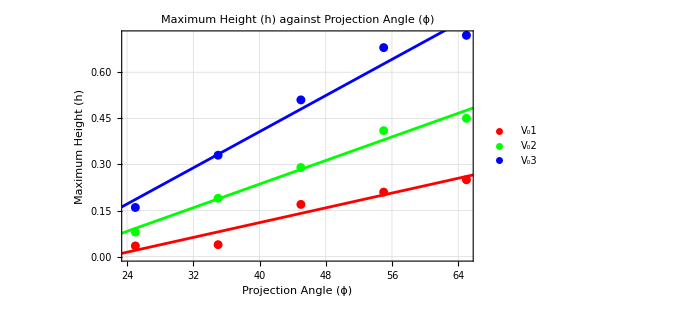
-Graphics-
V₀1: y==0.00601 x-0.12965
V₀2: y==0.0096 x-0.148
V₀3: y==0.0147 x-0.1815

```mathematica
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

errorV1={ErrorBar[0,#]&/@{0.005,0.005,0.002,0.002,0.002}};
errorV2={ErrorBar[0,#]&/@{0.010,0.015,0.020,0.025,0.030}};
errorV3={ErrorBar[0,#]&/@{0.015,0.020,0.025,0.030,0.035}};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines*)
combinedPlot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V₀1","V₀2","V₀3"}],ErrorListPlot[{Thread[{V1,errorV1}],Thread[{V2,errorV2}],Thread[{V3,errorV3}]}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle (ϕ)","Maximum Height (h)"},GridLines->Automatic,ImageSize->500,PlotLabel->"Maximum Height (h) against Projection Angle (ϕ)"];

fitEquations=Column[{Row[{"V₀1: ",eq1}],Row[{"V₀2: ",eq2}],Row[{"V₀3: ",eq3}]}];

Column[{combinedPlot,fitEquations}]
```

```mathematica
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

(*Error bars with central value and uncertainty*)
errorV1={Around[0.035,0.005],Around[0.039,0.005],Around[0.170,0.002],Around[0.210,0.002],Around[0.250,0.002]};
errorV2={Around[0.080,0.010],Around[0.190,0.015],Around[0.290,0.020],Around[0.410,0.025],Around[0.450,0.030]};
errorV3={Around[0.160,0.015],Around[0.330,0.020],Around[0.510,0.025],Around[0.680,0.030],Around[0.720,0.035]};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines*)
combinedPlot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V₀1","V₀2","V₀3"}],ErrorListPlot[{{V1,errorV1},{V2,errorV2},{V3,errorV3}}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle (ϕ)","Maximum Height (h)"},GridLines->Automatic,ImageSize->500,PlotLabel->"Maximum Height (h) against Projection Angle (ϕ)"];

fitEquations=Column[{Row[{"V₀1: ",eq1}],Row[{"V₀2: ",eq2}],Row[{"V₀3: ",eq3}]}];

Column[{combinedPlot,fitEquations}]
```

-Graphics-
V₀1: y==0.00601 x-0.12965
V₀2: y==0.0096 x-0.148
V₀3: y==0.0147 x-0.1815

```mathematica
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

errorV1={ErrorBar[0,#]&/@{0.005,0.005,0.002,0.002,0.002}};
errorV2={ErrorBar[0,#]&/@{0.010,0.015,0.020,0.025,0.030}};
errorV3={ErrorBar[0,#]&/@{0.015,0.020,0.025,0.030,0.035}};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Pad error lists to match the length of data lists*)
padErrors[data_,errors_]:=Thread[{data,PadRight[errors,Length[data],Automatic]}];

errorListV1=padErrors[V1,errorV1];
errorListV2=padErrors[V2,errorV2];
errorListV3=padErrors[V3,errorV3];

(*Plot the data and the best-fit lines*)
combinedPlot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V₀1","V₀2","V₀3"}],ErrorListPlot[{errorListV1,errorListV2,errorListV3}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle (ϕ)","Maximum Height (h)"},GridLines->Automatic,ImageSize->500,PlotLabel->"Maximum Height (h) against Projection Angle (ϕ)"];

fitEquations=Column[{Row[{"V₀1: ",eq1}],Row[{"V₀2: ",eq2}],Row[{"V₀3: ",eq3}]}];

Column[{combinedPlot,fitEquations}]
```

-Graphics-
V₀1: y==0.00601 x-0.12965
V₀2: y==0.0096 x-0.148
V₀3: y==0.0147 x-0.1815

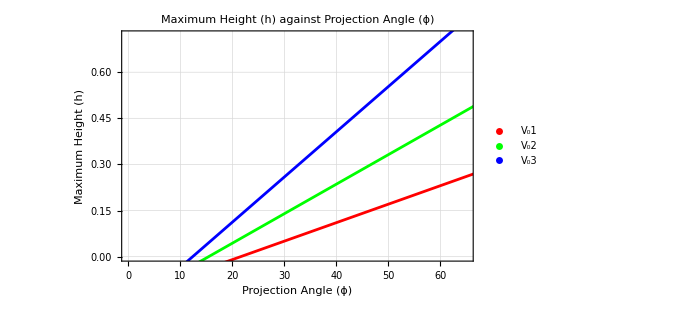

-Graphics-
V₀1: y==0.00601 x-0.12965
V₀2: y==0.0096 x-0.148
V₀3: y==0.0147 x-0.1815

```mathematica
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

errorV1={0.005,0.005,0.002,0.002,0.002};
errorV2={0.010,0.015,0.020,0.025,0.030};
errorV3={0.015,0.020,0.025,0.030,0.035};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Combine data and errors for each dataset*)
dataWithErrorV1=Transpose[{V1,ErrorBar[0,#]&/@errorV1}];
dataWithErrorV2=Transpose[{V2,ErrorBar[0,#]&/@errorV2}];
dataWithErrorV3=Transpose[{V3,ErrorBar[0,#]&/@errorV3}];

(*Plot the data and the best-fit lines*)
combinedPlot=Show[ListPlot[{dataWithErrorV1,dataWithErrorV2,dataWithErrorV3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V₀1","V₀2","V₀3"}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle (ϕ)","Maximum Height (h)"},GridLines->Automatic,ImageSize->500,PlotLabel->"Maximum Height (h) against Projection Angle (ϕ)"]

fitEquations=Column[{Row[{"V₀1: ",eq1}],Row[{"V₀2: ",eq2}],Row[{"V₀3: ",eq3}]}];

Column[{combinedPlot,fitEquations}]
```

```mathematica
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

errorV1=ErrorBar@@@{{0,0.505},{0,0.505},{0,0.502},{0,0.502},{0,0.002}};
errorV2=ErrorBar@@@{{0,0.010},{0,0.015},{0,0.020},{0,0.025},{0,0.030}};
errorV3=ErrorBar@@@{{0,0.015},{0,0.020},{0,0.025},{0,0.030},{0,0.035}};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines*)
combinedPlot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V₀1","V₀2","V₀3"}],ErrorListPlot[{{V1,errorV1},{V2,errorV2},{V3,errorV3}}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle (ϕ)","Maximum Height (h)"},GridLines->Automatic,ImageSize->500,PlotLabel->"Maximum Height (h) against Projection Angle (ϕ)"];

fitEquations=Column[{Row[{"V₀1: ",eq1}],Row[{"V₀2: ",eq2}],Row[{"V₀3: ",eq3}]}];

Column[{combinedPlot,fitEquations}]
```

-Graphics-
V₀1: y==0.00601 x-0.12965
V₀2: y==0.0096 x-0.148
V₀3: y==0.0147 x-0.1815

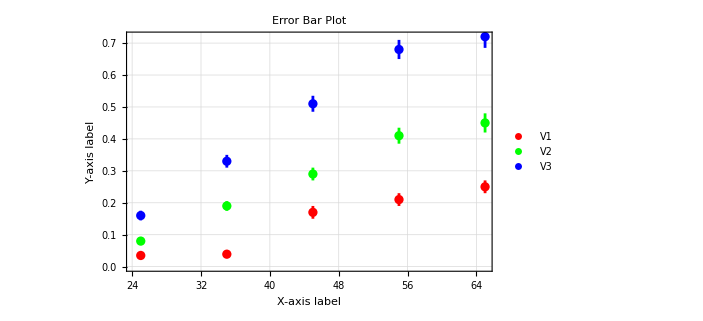

```mathematica
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

errorV1={0.005,0.005,0.02,0.02,0.02};
errorV2={0.010,0.015,0.020,0.025,0.030};
errorV3={0.015,0.020,0.025,0.030,0.035};

dataWithErrorV1=Transpose[{V1,ErrorBar@@@Transpose[{ConstantArray[0,Length[V1]],errorV1}]}];
dataWithErrorV2=Transpose[{V2,ErrorBar@@@Transpose[{ConstantArray[0,Length[V2]],errorV2}]}];
dataWithErrorV3=Transpose[{V3,ErrorBar@@@Transpose[{ConstantArray[0,Length[V3]],errorV3}]}];

(*Plot the data with error bars*)
ErrorListPlot[{dataWithErrorV1,dataWithErrorV2,dataWithErrorV3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V1","V2","V3"},Frame->True,FrameLabel->{"X-axis label","Y-axis label"},GridLines->Automatic,PlotLabel->"Error Bar Plot"]
```